```mathematica
BlochSphere = {{Opacity[0.2],Sphere[]},{EdgeForm[{Dashed,Black}],FaceForm[None],
Cylinder[{{0,0,-.001},{0,0,.001}}]},
{Line[{{0,0,0},{1,0,0}}]},{Line[{{0,0,0},{0,1,0}}]},{Line[{{0,0,0},{0,0,1}}]},
{Line[{{0,0,0},{-1,0,0}}]},{Line[{{0,0,0},{0,-1,0}}]},{Line[{{0,0,0},{0,0,-1}}]},
{PointSize[0.01],Map[Point,{{0,0,1},{0,1,0},{1,0,0},{0,0,-1},{0,-1,0},{-1,0,0}}]},
Text[Style["+",18],{1.4,0,0}],Text[Style["i",18],{0,1.4,0}],Text[Style["0",18],{0,0,1.4}],
Text[Style["-",18],{-1.4,0,0}],Text[Style["-i",18],{0,-1.4,0}],Text[Style["1",18],{0,0,-1.4}]
};
showBlochVector[a_]:={α=a/Norm[a];Graphics3D[{BlochSphere,{Red,Arrow[Tube[{{0,0,0},α}]]},
{Red,Sphere[{{α[[1]],0,0},{0,α[[2]],0},{0,0,α[[3]]}},0.02]}
},Boxed->False,ImageSize->600]};
showBlochVectors[a_,b_]:={α=a/Norm[a];β=b/Norm[b];Graphics3D[{BlochSphere,{Red,Arrow[Tube[{{0,0,0},α}]]},{Blue,Arrow[Tube[{{0,0,0},β}]]},
{Red,Sphere[{{α[[1]],0,0},{0,α[[2]],0},{0,0,α[[3]]}},0.02]}
},Boxed->False,ImageSize->600]}
showBlochVector[{-1,-1,2}]
```

{-Graphics3D-}

```mathematica
Manipulate[{},]
```

```mathematica
Export["spheranim.gif",Out[191]]
```

spheranim.gif

```mathematica
mov=Table[showBlochVectors[{-Cos[θ+π/4],0,Sin[θ+π/3]},{0,-1,0}],{θ,0,2 π,2 π/50}];
Export["movie.gif",mov]
```

movie.gif

```mathematica
Cos[π/3]
```

1/2

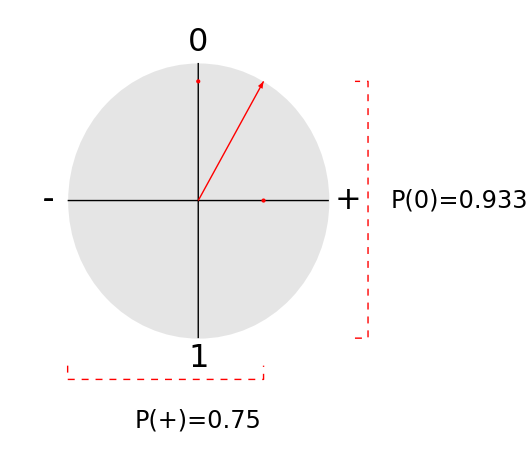

```mathematica
θ=π/3;Graphics[{
{Opacity[0.2],Gray,Disk[]},
{Black,Thick,Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]},
{Red,Thick,Arrow[{{0,0},{Cos[θ],Sin[θ]}}]},
{Red,PointSize[Large],Point[{0,Sin[θ]}],Red,PointSize[Large],Point[{Cos[θ],0}]},
{Text[Style["0",32],{0.,1.15}],Text[Style["1",32],{0.,-1.15}]},
{Text[Style["+",32],{1.15,0}],Text[Style["-",32],{-1.15,0}]},
{Dashed,Thick,Red,Line[{{1.2,-1},{1.3,-1},{1.3,Sin[θ]},{1.2,Sin[θ]}}]},
{Dashed,Thick,Red,Line[{{-1,-1.2},{-1,-1.3},{Cos[θ],-1.3},{Cos[θ],-1.2}}]},
{Text[Style["P(0)=0.933",24],{2,0}],Text[Style["-",32],{-1.15,0}]},
{Text[Style["P(+)=0.75",24],{0,-1.6}],Text[Style["-",32],{-1.15,0}]}
}]
```

```mathematica
N[1/2+1/4]
```

0.75